```mathematica
ClearAll[c,G,MSun,rhoRadBBN];

c=29979245800;                   (*velocidad de la luz:cm/s*)
G=66743/10^12;                   (*constante gravitacional:cm^3/(g s^2)*)
MSun=198847*10^28;               (*masa solar:g*)

rhoRadBBN=7331305019814086*10^11;
(*densidad de energía de radiación en BBN:erg/cm^3*)
```

```mathematica
ti=37/50;                       (*coordenada temporal de BBN:0.74 s*)
ai=83/500000000000;             (*factor de escala en BBN:1.66*10^-10*)
Hti=67/100;                     (*parámetro de Hubble en BBN:0.67 s^-1*)
```

```mathematica
ρ0[ξ_]:= ξ*rhoRadBBN
```

```mathematica
Cxi[ξ_]:= (4π G)/(3c^2)*ρ0[ξ]
```

```mathematica
ClearAll[sol];
```

```mathematica
tMin=-5;
(* n = -1 luego 
(Y[t])^((n-1)/2) ----> Y^-1
*)
```

```mathematica
ClearAll[sol,tBounce]
```

```mathematica
sol[ξ_]:=sol[ξ]=NDSolve[{Y'[t]==v[t],v'[t]==2*Cxi[ξ]*(Y[t])^(-1),Y[ti]==1,v[ti]==2*Hti,WhenEvent[v[t]==0,"StopIntegration","LocationMethod"->"Brent"]},{Y,v},{t,-1,ti},WorkingPrecision->40,AccuracyGoal->25,PrecisionGoal->25,MaxStepSize->1/1000,MaxSteps->Infinity];
```

```mathematica
tBounce[ξ_]:=tBounce[ξ]=(Y/. sol[ξ][[1]])["Domain"][[1,1]];
```

```mathematica
tB= tBounce[1/10]
```

-0.02689614804598900925735308156438611042608

```mathematica
Yfunc[ξ_,t_]:=Y[t]/. sol[ξ][[1]];
vFunc[ξ_,t_]:=v[t]/. sol[ξ][[1]];
```

```mathematica
apos[ξ_, t_]:=ai*Sqrt[Y[t+tBounce[ξ]]/. sol[ξ][[1]]];
```

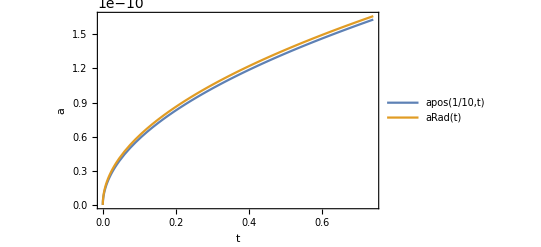

```mathematica
ar := ai/ti^(1/2)
aRad[t_]:= ar*t^(1/2)
Plot[{apos[1/10, t],aRad[t]},{t,0,ti},AxesLabel->{"t","a"},Frame->True,PlotRangePadding->0, PlotLegends->"Expressions"]
```